```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
file=OpenRead["mechanisms/pyrolysis.cti"];
test=ReadList[file,"String"];
Close[file];
slst=StringSplit[Extract[test,Position[test,u_/;StringQ[u]&&First[StringSplit[u,"("]]=="species"]],"'"][[All,2]];
alst=Partition[#,2]&/@StringSplit[StringTrim[StringSplit[Extract[test,Position[test,u_/;StringQ[u]&&First[StringSplit[u,"("]]=="species"]+1],"'"][[All,2]]],{":"," "}];
sensitivities=Flatten[Import["data/pyrolysis/ms.dat"]];
```

/Users/zack/Documents/ignition/cantera/ratemeasure

### Full model ignition peaks

data/pyrolysis/

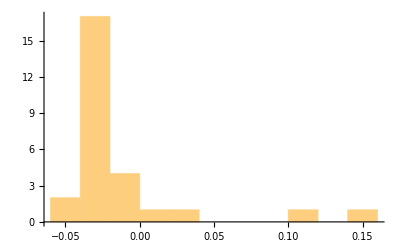

-0.0134742

0.0443372

{0.934465,0.960552,0.946404,0.929844,0.947554,0.927989,0.926672,0.938645,0.913544,0.952075,0.940649,0.933659,1.03792,0.933397,0.917629,1.05443,0.927849,0.90562,0.9197,0.978236,0.931327,1.26332,0.973258,0.919175,1.43038,0.966334,0.90947}

1.43038

0.90562

```mathematica
filebase="data/pyrolysis/"
individuals=First/@DeleteCases[Table[Import[filebase<>"individual/"<>ToString[i]<>"norms.dat"],{i,1,27}],{}];
Histogram[Log[DeleteCases[individuals,{}][[All,6]]]/Log[10]]
Mean[Log[individuals[[All,6]]]/Log[10]]
StandardDeviation[Log[individuals[[All,6]]]/Log[10]]
N[individuals[[All,6]],3]
Max[individuals[[All,6]]]
Min[individuals[[All,6]]]
```

```mathematica
itimes={};
imaxes={};
h2yields={};
ch4yields={};
plots={};

Monitor[Do[
filebase="data/pyrolysis/individual/"<>ToString[n];
species=Import[filebase<>"species.dat"][[1]];
ind=First@FirstPosition[species,"H2"];
ind2=First@FirstPosition[species,"CH4"];
ns=Length[species];
times=BinaryReadList[filebase<>"times_"<>ToString[0]<>".npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures_"<>ToString[0]<>".npy","Real64"][[17;;-1]];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"moles_"<>ToString[0]<>".npy","Real64"][[17;;-1]],ns]];
ig=First@FirstPosition[concentrations[[ind]],u_/;u>0.99*concentrations[[ind,-1]]];
AppendTo[itimes,times[[ig]]];
AppendTo[h2yields,concentrations[[ind,-1]]];
AppendTo[ch4yields,concentrations[[ind2,-1]]];
AppendTo[plots,
ListPlot[Transpose[{times,concentrations[[ind]]}],PlotStyle->Directive[Black],PlotRange->All,Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (ms)",DisplayForm[RowBox[{Subscript[X,O],"×",10^HoldForm[5]}]]},ImagePadding->{{75,5},{75,5}},ImageSize->250,AspectRatio->1,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],Epilog->{Red,AbsoluteThickness[2],Line[{{times[[ig]],0},{times[[ig]],concentrations[[ind,ig]]}}]}]];,{n,1,27}],n]
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

```mathematica
ScientificForm[2*itimes,3]
ScientificForm[h2yields,2]
ScientificForm[ch4yields,2]
```

{5.06×10^5,1.91×10^4,5.04×10^2,1.85×10^5,5.29×10^3,1.21×10^2,9.36×10^4,2.33×10^3,5.48×10^1,9.43×10^4,4.11×10^3,1.16×10^2,4.96×10^4,1.6×10^3,3.91×10^1,3.05×10^4,8.5×10^2,1.99×10^1,3.42×10^4,1.28×10^3,3.92×10^1,2.09×10^4,6.44×10^2,1.67×10^1,1.41×10^4,3.88×10^2,9.36}

{2.8×10^-1,2.6×10^-1,2.1×10^-1,4.×10^-1,3.7×10^-1,3.1×10^-1,5.1×10^-1,4.7×10^-1,4.×10^-1,2.8×10^-1,2.7×10^-1,2.3×10^-1,4.×10^-1,3.8×10^-1,3.3×10^-1,5.1×10^-1,4.8×10^-1,4.2×10^-1,2.8×10^-1,2.7×10^-1,2.4×10^-1,4.×10^-1,3.8×10^-1,3.4×10^-1,5.×10^-1,4.8×10^-1,4.3×10^-1}

{1.2×10^-2,3.2×10^-2,6.5×10^-2,1.9×10^-2,4.7×10^-2,9.5×10^-2,2.6×10^-2,6.2×10^-2,1.2×10^-1,1.×10^-2,2.4×10^-2,5.4×10^-2,1.7×10^-2,3.7×10^-2,8.×10^-2,2.3×10^-2,5.1×10^-2,1.1×10^-1,8.9×10^-3,2.×10^-2,4.4×10^-2,1.5×10^-2,3.1×10^-2,6.7×10^-2,2.1×10^-2,4.3×10^-2,8.9×10^-2}

{679,142,476,445,147,39,685,131,105,70}

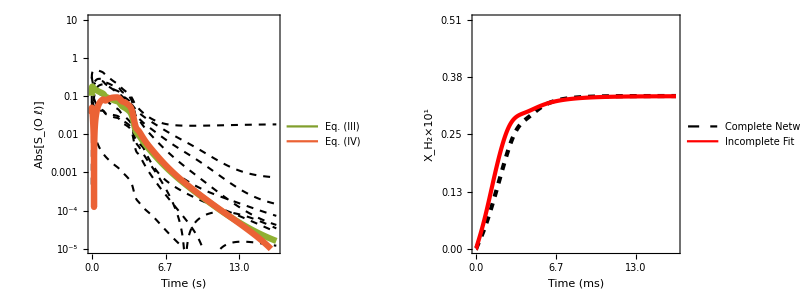

plots/figs2.pdf

```mathematica
n=23;
filebase="data/pyrolysis/";
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
tmax=times[[-1]];
species=Import[filebase<>"species.dat"][[1]];
nspecies=Length[species];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"moles_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
Nt=Length[times];
rates=BinaryReadList[filebase<>"rates_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
nreactions=Length[rates]/Nt;
rates=Transpose[Partition[rates,nreactions]];
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
sensitivities=Mean[Table[Transpose[Partition[BinaryReadList[filebase<>"sensitivities_"<>ToString[m]<>".npy","Real64"][[17;;-1]],nreactions]],{m,0,26}]];
fit=Transpose[Partition[BinaryReadList[filebase<>"fit_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
ind=First@FirstPosition[species,"H2"];

cmax=1.5*Max[concentrations[[ind]],fit[[ind]]];
topsens=Table[FirstPosition[Table[Norm[sensitivities[[i]],Infinity],{i,1,Length[sensitivities]}],Extract[Sort[Table[Norm[sensitivities[[i]],Infinity],{i,1,Length[sensitivities]}]],-i]][[1]],{i,1,10}]
p4=ListPlot[{concentrations[[ind]],fit[[ind]]},PlotStyle->{Directive[Thickness[0.01],Black,Dashed],Directive[Thickness[0.01],Red]},PlotRange->{All,{0,cmax}},Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (ms)",DisplayForm[RowBox[{Subscript[X,Subscript[H,2]],"×",10^HoldForm[1]}]]}, FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,cmax,(cmax)/4}],{}},{Table[{i,PaddedForm[tmax*i/(Nt-1),{2,1}]},{i,0,(Nt-1),(Nt-1)/5}],{}}},ImageSize->300,ImagePadding->{{65,20},{55,10}},AspectRatio->1,PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Red},{Style[Column[{"Complete","Network"}],Background->White],Style[Column[{"Incomplete","Fit"}],Background->White]},LabelStyle->Directive[14],LegendMarkerSize->{{25,10}},LegendLayout->"Row"],{Scaled[{0.01,0.95}],Scaled[{0,1}]}],FrameStyle->Directive[Black,AbsoluteThickness[1.5]]];
eq1=679;
eq2=684;
p5=Legended[ListLogPlot[Join[Abs[Part[sensitivities,Complement[topsens,{eq2,eq1}]]],{Abs[sensitivities[[eq2]]]*1.2,Abs[sensitivities[[eq1]]]*0.8}],PlotStyle->Join[Table[Directive[Thickness[0.005],Dashed,Black],{i,1,Length[topsens]-2}],{Directive[Thickness[0.015],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.015],ColorData[97,"ColorList"][[4]]]}],PlotRange->{1*10^-5,1*10^1},Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (s)", Abs[Subscript[S,DisplayForm[RowBox[{O," ",ℓ}]]]]}, FrameTicks->{{Table[With[{n=n},{10^n,HoldForm[10^HoldForm[n]]}],{n,-3,3, 2}],{}},{Table[{i,PaddedForm[tmax*i/(Nt-1),{2,1}]},{i,0,(Nt-1),(Nt-1)/5}],{}}},ImageSize->300,ImagePadding->{{65,20},{55,10}},AspectRatio->1,FrameStyle->Directive[Black,AbsoluteThickness[1.5]]],Placed[LineLegend[{Darker[ColorData[97,"ColorList"][[3]],0.1],ColorData[97,"ColorList"][[4]]},{"Eq. (III)  ","Eq. (IV)  "},LabelStyle->Directive[14],LegendMarkerSize->{{25,10}},LegendLayout->"Row"],{Scaled[{0.05,0.95}],Scaled[{0,1}]}]];
p=Grid[{{p5,p4}}]
Export["plots/figs2.pdf",p]
```

### Graph plots

22758

{RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[1, Rational[1, 3], Rational[1, 3]]}

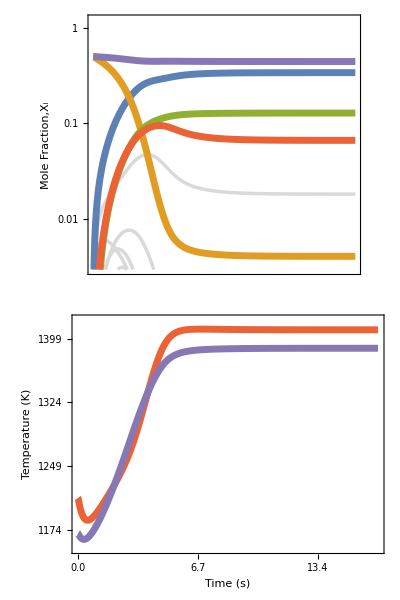

```mathematica
n=23;
filebase="data/pyrolysis/";
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
tmax=times[[-1]];
species=Import[filebase<>"species.dat"][[1]];
nspecies=Length[species];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"moles_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
Nt=Length[times];
rates=BinaryReadList[filebase<>"rates_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
nreactions=Length[rates]/Nt;
rates=Transpose[Partition[rates,nreactions]];
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
fit=Transpose[Partition[BinaryReadList[filebase<>"fit_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
ind=First@FirstPosition[species,"H2"];

imagePadding2={{75,75},{1,1}};
imgSize2={500,250};
imagePadding1={{75,75},{50,1}};
imgSize1={500,290};
imgSize3={440*(2.2)/(1.3),440};

sptime[text_]:=First@FirstPosition[Accumulate[10^-12+concentrations[[First@FirstPosition[species,text]]]]/Total[10^-12+concentrations[[First@FirstPosition[species,text]]]],u_/;u>0.5]/Nt
sptimemin=Min[sptime/@species];
sptimemax=Max[sptime/@species];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)]
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8


Nt=Length[times];
Tmax=Max[temperatures];
Tmin=Min[temperatures];
Pmax=Max[pressures];
Pmin=Min[pressures];

reactantnames={"C2H6"};
productnames={"H2","CH4"};
cmax=1.1*Max[{concentrations[[First@FirstPosition[species,"C2H6"]]],concentrations[[First@FirstPosition[species,"H2"]]][[2]],concentrations[[First@FirstPosition[species,"CH4"]]][[2]]}];
cplots={"H2","C2H4","C6H6","CH4", "N2"};
ccplots=ColorData[97,"ColorList"][[1;;5]];
p1=ListLogPlot[Join[concentrations,(concentrations[[First@FirstPosition[species,#]]])&/@cplots],Joined->True,PlotRange->{3*10^-3,1.2},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{None,DisplayForm[RowBox[{"Mole Fraction,",Subscript[ X,i]}]]},FrameTicks->{{Automatic,{}},Table[{i,""},{i,0,(Nt-1),(Nt-1)/5}]},PlotStyle->Join[ConstantArray[Directive[Thickness[0.005],LightGray],nspecies],Directive[Thickness[0.01],#]&/@ccplots],Prolog->Join[Inset[Framed[Style[DisplayForm[ToBoxes@Row[Subscript[#[[1]],#[[2]]/."1"->""]&/@SortBy[Extract[alst,FirstPosition[slst,#[[1]]]],First]]],16,#[[2]]],Background->None,FrameStyle->None],{Nt*1.1,Log[concentrations[[First@FirstPosition[species,#[[1]]],-1]]]+If[#[[1]]=="N2",0.2,0]}]&/@Transpose[{cplots,ccplots}]],ImagePadding->imagePadding2,ImageSize->imgSize2,AspectRatio->Last[imgSize1]/First[imgSize1],FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRangeClipping->False];
p2=ListPlot[{(temperatures-Tmin)/(Tmax-Tmin)+0.05,(pressures-Pmin)/(Pmax-Pmin)-0.05},Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[4]],Thickness[0.01]],Directive[ColorData[97,"ColorList"][[5]],Thickness[0.01]]},PlotRange->{-0.1,1.1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{{Style["Temperature (K)",ColorData[97,"ColorList"][[4]]],Style["Pressure (atm)",ColorData[97,"ColorList"][[5]]]},{"Time (s)",None}},FrameTicks->{{Table[{(T-Tmin)/(Tmax-Tmin),Style[Round[T],ColorData[97,"ColorList"][[4]]]},{T,Tmin,Tmax,(Tmax-Tmin)/3}],Table[{(P-Pmin)/(Pmax-Pmin),Style[PaddedForm[P/101325.,{3,2}],ColorData[97,"ColorList"][[5]]]},{P,Pmin,Pmax,(Pmax-Pmin)/3}]},{Table[{i,PaddedForm[tmax*i/(Nt-1),{4,1}]},{i,0,(Nt-1),(Nt-1)/5}],{}}},ImagePadding->imagePadding1,ImageSize->imgSize1,AspectRatio->Last[imgSize1]/First[imgSize1],FrameStyle->Directive[Black,AbsoluteThickness[1.5]]];
(* Possible bimolecular interactions *)
reacs=Flatten[Table[{i,j},{i,1,Length[alst]},{j,i,Length[alst]}],1];
atoms=DeleteDuplicates[Flatten[alst[[All,All,1]]]];
acount[r_]:=(Total[ToExpression/@Cases[Flatten[alst[[r[[{1,2}]]]],1],u_/;u[[1]]==#][[All,2]]]&/@atoms);
test=acount/@reacs;
test2=Cases[Position[test,#]&/@DeleteDuplicates[test],u_/;Length[u]>1];
stoipairs=slst[[#]]&/@#&/@(Extract[reacs,#]&/@test2);
stoipairs2=Flatten[Subsets[#,{2,2}]&/@stoipairs,1];
Total[Binomial[#,2]&/@(Length/@stoipairs)]
colors={Lighter[Blue],Lighter[Red]}
Grid[{{p1},{p2}}]
```

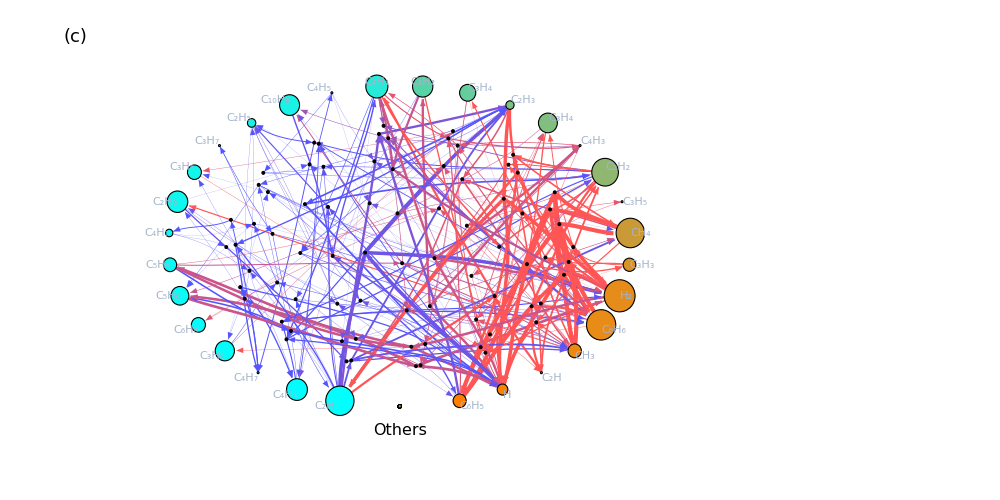
-Graphics- | -Graphics-

```mathematica
r1=1.5;
r2=1;
weights=Mean/@rates;
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates/Nt;
reactants=Import[filebase<>"reactants.dat"][[All,1;;-1;;2]];
products=Import[filebase<>"products.dat"][[All,1;;-1;;2]];
wscale=Max[Abs[weights]];
ethrs=Mean[Abs[weights]]/2;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[Abs[weights[[i]]]>ethrs,If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{}],{i,1,nreactions}];
vertices=Union[species,DeleteDuplicates[Flatten[edges][[All,1]],Flatten[edges][[All,2]]]];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
transform[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin)/(ymax-ymin)-1/2,(p[[1]]-xmin)/(xmax-xmin)-1/2};
transform2[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin2)/(ymax2-ymin2)-1/2,(p[[1]]-xmin2)/(xmax2-xmin2)-1/2};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[ethrs*Exp[i*1.0/5*(-Log[Abs[ethrs/wscale]])],{i,5,1,-1}];
vcs=Join[Table[centerspecies[[i]]->{r1*Cos[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)],r2*Sin[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)]},{i,1,Length[centerspecies]}],
Table[bottomspecies[[i]]->{0,-r2},{i,1,Length[bottomspecies]}],Table[i->If[MemberQ[centerreactions,i],transform[rvcs[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]>ethrs]],weights2[[#]]&],i]]]],transform2[rvcs2[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],weights2[[#]]&],i]]]]],{i,nreactions}]];

p0=Graph[vertices,Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[ValueQ[Element[#,Integers]],None,If[MemberQ[centerspecies,#],If[0.0015*ImageDimensions[Rasterize[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->LightGray,FrameStyle->None,RoundingRadius->5,ContentPadding->False]]][[1]]<vsize[#]&&False,Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center],Center],Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center,ContentPadding->False],{{1/2,1/2},{1/2,1/2}-(#/Norm[#]/.vcs)}]],None]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{Graphics[Text[Style["Nodes",16],{0,0}],ImageSize->{125,50}],Graphics[Text[Style["Links",16],{0,0}],ImageSize->{125,50}]},{MatrixPlot[Table[Blend[{Cyan,Orange},(y-sptimemin)/(sptimemax-sptimemin)],{y,sptimemin,sptimemax,(sptimemax-sptimemin)/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{90,15},{10,5}},FrameTicks->{{Table[{i,PaddedForm[(sptimemin+(i-1)*(sptimemax-sptimemin)/100)*times[[-1]],{4,1}]},{i,1,101,20}],None},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{"Species Time (s)",None}},RotateLabel->True,DataReversed->{True,True}],MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)*times[[-1]],{4,1}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (s)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}],Graphics[{{Table[{Thickness[10*Abs[ethick*(Log[Abs[wsizes[[i]]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Line[{{1,-1.25*i},{2,-1.25*i}}],Text[Style[PaddedForm[10^3*wsizes[[i]],{2,2}],16],{3,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style[DisplayForm[RowBox[{"Rate ","(","mol ",Superscript["m",-3],Superscript["s",-1],")"}]],16],{4.9,-4}],Pi/2]},PlotRange->{{0.5,6},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}],Text[Style["Others",16],{0,-r2-0.15}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->0]
Export["plots/figs3.pdf",p3,LineBreakWithin->False];
```

```mathematica
n0=400;
n1=1600;
dn=4;
AbsoluteTiming[Monitor[Do[
weights3=rates[[All,n]]/10;
vsize[text_]:=0.005+0.08*(Log[Max[concentrations[[First@FirstPosition[species,text],n]],10^-8]]/Log[10]+8)/8;
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights3[[edge[[1]]]],weights3[[edge[[2]]]]];
p0=Graph[vertices,Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[ValueQ[Element[#,Integers]],None,If[MemberQ[centerspecies,#],If[0.0015*ImageDimensions[Rasterize[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->LightGray,FrameStyle->None,RoundingRadius->5,ContentPadding->False]]][[1]]<vsize[#]&&False,Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center],Center],Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center,ContentPadding->False],{{1/2,1/2},{1/2,1/2}-(#/Norm[#]/.vcs)}]],None]]&/@vertices),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@vertices),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@vertices),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{Graphics[Text[Style["Nodes",16],{0,0}],ImageSize->{125,50}],Graphics[Text[Style["Links",16],{0,0}],ImageSize->{125,50}]},{MatrixPlot[Table[Blend[{Cyan,Orange},(y-sptimemin)/(sptimemax-sptimemin)],{y,sptimemin,sptimemax,(sptimemax-sptimemin)/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{90,15},{10,5}},FrameTicks->{{Table[{i,PaddedForm[(sptimemin+(i-1)*(sptimemax-sptimemin)/100)*times[[-1]],{4,1}]},{i,1,101,20}],None},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{"Species Time (s)",None}},RotateLabel->True,DataReversed->{True,True}],MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)*times[[-1]],{4,1}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (s)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}],Graphics[{{Table[{Thickness[10*Abs[ethick*(Log[Abs[wsizes[[i]]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Line[{{1,-1.25*i},{2,-1.25*i}}],Text[Style[PaddedForm[10^3*wsizes[[i]],{2,2}],16],{3,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style[DisplayForm[RowBox[{"Rate ","(","mol ",Superscript["m",-3],Superscript["s",-1],")"}]],16],{4.9,-4}],Pi/2]},PlotRange->{{0.5,6},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}],Text[Style["Others",16],{0,-r2-0.15}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]],Dashed,AbsoluteThickness[2.0],Line[{{n,Log[10^-16]},{n,0}}]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]],Dashed,AbsoluteThickness[2.0],Line[{{n,-0.1},{n,1.1}}]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->2];
If[n==n0,Export["plots/figs6.pdf",p3]];Export["panimation/"<>IntegerString[(n-n0)/dn,10,4]<>".png",p3,ImageSize->4000];,{n,n0,n1,dn}],n]]
```

Export::nodir: Directory /Users/zack/Documents/ignition/cantera/ratemeasure/panimation/ does not exist.

Export::noopen: Cannot open panimation/0000.png.

$Aborted

### Correlations, density plots, and histograms

```mathematica
rlst1=Import["data/pyrolysis/sweepnorms.dat"];
```

```mathematica
filebase="data/pyrolysis/";
asenses=Flatten[Import[filebase<>"ms.dat"]];
Print["S-e"]
Correlation/@{Transpose[{Cases[rlst1,u_/;u[[1]]==678&&u[[6]]≠"failed"][[All,5]]/asenses[[679]],Log[Cases[rlst1,u_/;u[[1]]==678&&u[[6]]≠"failed"][[All,7]]]/Log[10]}],Transpose[{Cases[rlst1,u_/;u[[1]]==683&&u[[6]]≠"failed"][[All,5]]/asenses[[684]],Log[Cases[rlst1,u_/;u[[1]]==683&&u[[6]]≠"failed"][[All,7]]]/Log[10]}]}

Print["S-k"]
Correlation/@{Transpose[{Cases[rlst1,u_/;u[[1]]==678&&u[[6]]≠"failed"][[All,5]]/asenses[[679]],Abs[Log[Cases[rlst1,u_/;u[[1]]==678&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}],Transpose[{Cases[rlst1,u_/;u[[1]]==683&&u[[6]]≠"failed"][[All,5]]/asenses[[684]],Abs[Log[Cases[rlst1,u_/;u[[1]]==683&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}]}

Print["k-e"]
Correlation/@{Transpose[{Log[Cases[rlst1,u_/;u[[1]]==678&&u[[6]]≠"failed"][[All,7]]],Abs[Log[Cases[rlst1,u_/;u[[1]]==678&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}],Transpose[{Log[Cases[rlst1,u_/;u[[1]]==683&&u[[6]]≠"failed"][[All,7]]]/Log[10],Abs[Log[Cases[rlst1,u_/;u[[1]]==683&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}]}
```

S-e

{{{1.,0.585715},{0.585715,1.}},{{1.,0.465446},{0.465446,1.}}}

S-k

{{{1.,0.473088},{0.473088,1.}},{{1.,0.447994},{0.447994,1.}}}

k-e

{{{1.,0.318819},{0.318819,1.}},{{1.,0.642387},{0.642387,1.}}}

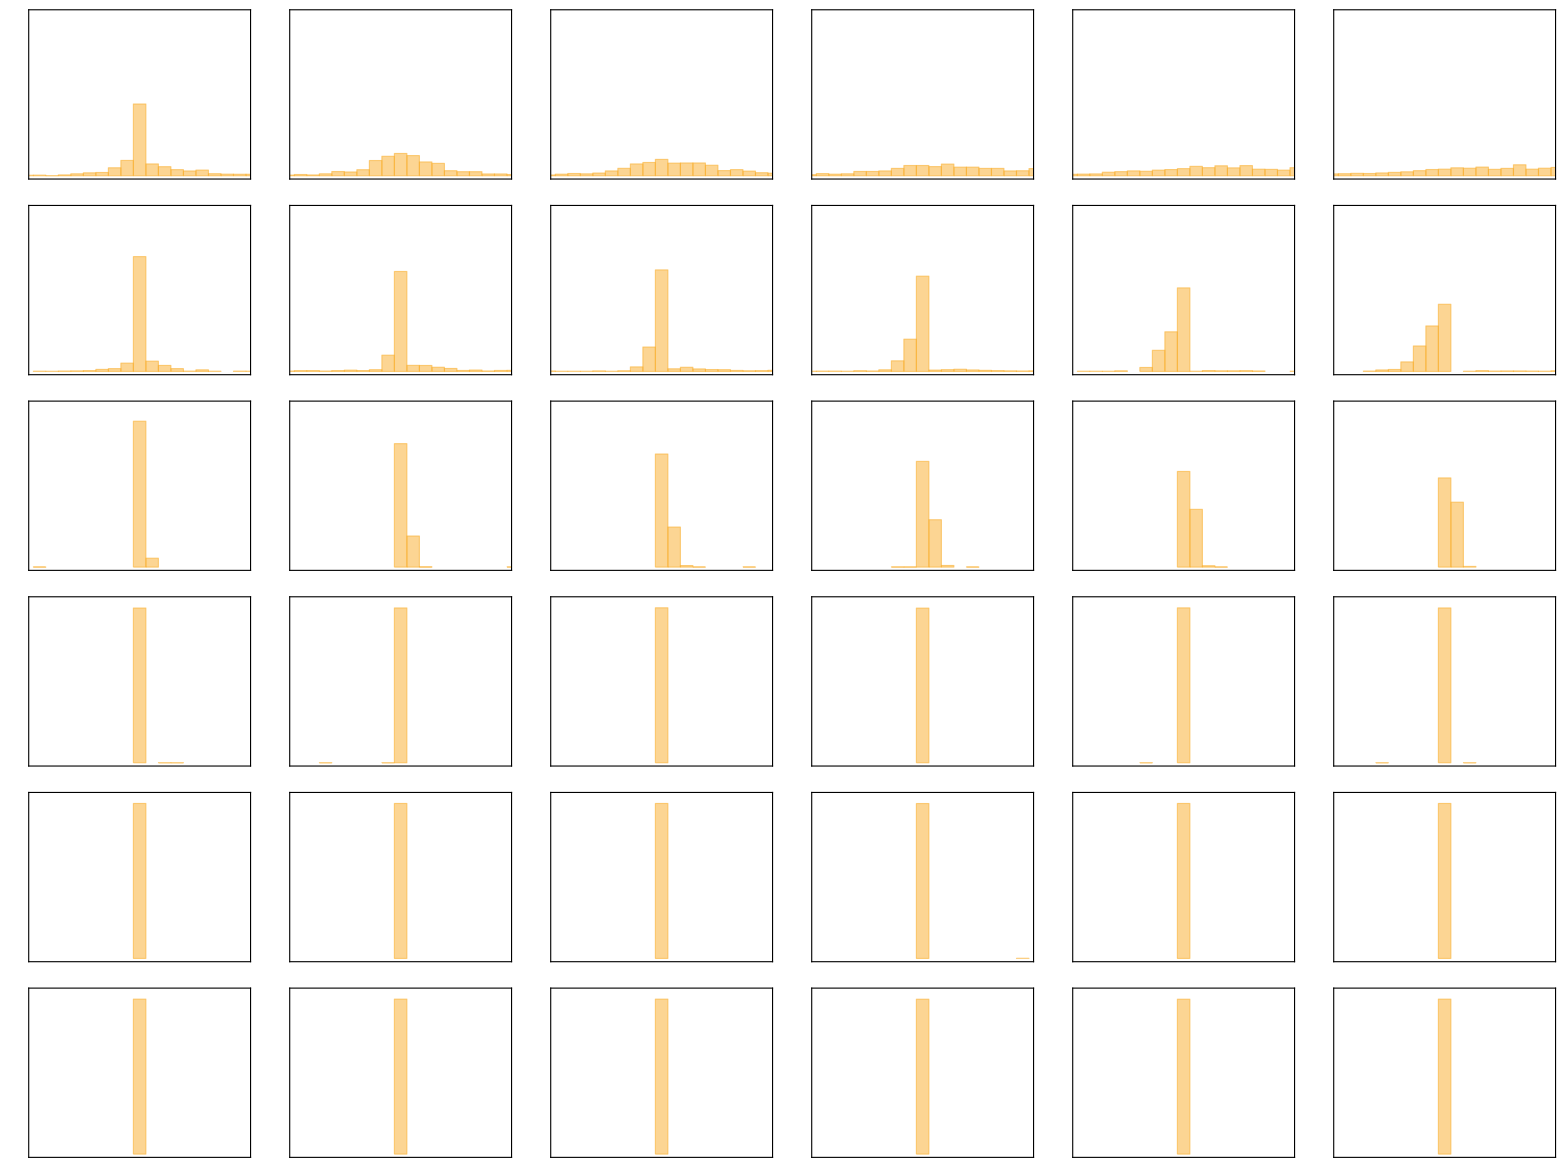

plots/phistograms.pdf

```mathematica
p=Grid[Table[ticks={{If[remove==10,Table[{i,PaddedForm[i,{2,2}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]],Table[{i,""},{i,0,1,0.2}]},{If[keep==160,Table[{i,Round[10*i]},{i,-0.5,0.5,0.2}],Table[{i,""},{i,-0.5,0.5,0.2}]],Table[{i,""},{i,-0.5,0.5,0.2}]}};
labels={{If[remove==10,"Proportion",None],If[remove==160,Subscript[N,"ret"]==keep,None]},{If[keep==160,Subscript[Δk,"ratio"]*10,None],If[keep==10,Subscript[N,"rem"]==remove,None]}};
imageSize={If[remove==10||remove==160,250,250-70],If[keep==160||keep==10,220,220-40]};
imagePadding={{If[remove==10,75,5],If[remove==160,55,5]},{If[keep==160,55,10],If[keep==10,35,1]}};Histogram[{Log[Cases[rlst1,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10]},{-1,1,2/31.},"Probability",Axes->False,Frame->True,FrameTicks->ticks,FrameLabel->labels,LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1.5],Black],PlotRange->{{-0.55,0.55},{0,1.05}},AspectRatio->1,ImageSize->imageSize,ImagePadding->imagePadding,PlotRangeClipping->True],{keep,40, 840, 160},{remove,40, 840, 160}],Spacings->0]
Export["plots/phistograms.pdf",p]
```

```mathematica
sensitivities=Flatten[Import["data/pyrolysis/ms.dat"]];
means37={};
errors37={};
means52={};
errors52={};
senses37={};
senses52={};
Monitor[Do[Do[
cases=Cases[rlst1,u_/;u[[1]]==678&&u[[3]]==remove&&u[[4]]==keep&&Last[u]≠"failed"];If[Length[cases]>0,AppendTo[means37,{keep,remove,Mean[Abs[Log[DeleteCases[cases[[All,6]],u_/;u=="failed"]]/Log[10]]]}];
AppendTo[errors37,{keep,remove,Mean[Log[DeleteCases[cases[[All,7]],u_/;u=="failed"]]/Log[10]]}];AppendTo[senses37,{keep,remove,Mean[DeleteCases[cases[[All,5]],u_/;u=="failed"]/sensitivities[[679]]]}];];cases=Cases[rlst1,u_/;u[[1]]==683&&u[[3]]==remove&&u[[4]]==keep&&Last[u]≠"failed"];If[Length[cases]>0,AppendTo[means52,{keep,remove,Mean[Abs[Log[DeleteCases[cases[[All,6]],u_/;u=="failed"]]/Log[10]]]}];
AppendTo[errors52,{keep,remove,Mean[Log[DeleteCases[cases[[All,7]],u_/;u=="failed"]]/Log[10]]}];AppendTo[senses52,{keep,remove,Mean[DeleteCases[cases[[All,5]],u_/;u=="failed"]/sensitivities[[684]]]}];];,{keep,40, 840, 80}];,{remove,40, 840, 80}],{keep,remove}]
```

```mathematica
p1=ListDensityPlot[means37,PlotRange->{0,1.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,"rem"],None},{None,"Eq. (III)"}},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]},{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]}},ImagePadding->{{55,10},{5,55}},AspectRatio->1/2];
p2=ListDensityPlot[means52,PlotRange->{0,1.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Eq. (IV)"}},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]},{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]}},ImagePadding->{{5,10},{5,55}},AspectRatio->1/2];
p3=ListDensityPlot[senses37,PlotRange->{0,10.0},ClippingStyle->Automatic,PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],Subscript[N,"rem"]},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]},{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]}},ImagePadding->{{55,10},{5,5}},AspectRatio->1/2];
p4=ListDensityPlot[senses52,PlotRange->{0,10.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],None},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]},{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]}},ImagePadding->{{5,10},{5,5}},AspectRatio->1/2];
p5=ListDensityPlot[errors37,PlotRange->{-2,0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],Subscript[N,"rem"]},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]},{Table[{i,i},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]}},ImagePadding->{{55,10},{55,5}},AspectRatio->1/2];
p6=ListDensityPlot[errors52,PlotRange->{-2,0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],None},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]},{Table[{i,i},{i,40, 840, 160}],Table[{i,""},{i,40, 840, 160}]}},ImagePadding->{{5,10},{55,5}},AspectRatio->1/2];
p=Grid[{{rasterizeBackground[p1],Grid[{{rasterizeBackground[p2],BarLegend[{"LightTemperatureMap",{0,1.0}},LabelStyle->Directive[Black,14],LegendLabel->Abs[DisplayForm[Subscript[log,10][RowBox[{Subscript[k,est],"/",Subscript[k,0]}]]]],ImageSize->{250,125}]}}]},{rasterizeBackground[p3],Grid[{{rasterizeBackground[p4],BarLegend[{"LightTemperatureMap",{0,10.0}},LabelStyle->Directive[Black,14],LegendLabel->DisplayForm[RowBox[{Subscript[S,"r"],"/",Subscript[S,"m"]}]],ImageSize->{250,125}]}}]},{rasterizeBackground[p5],Grid[{{rasterizeBackground[p6],BarLegend[{"LightTemperatureMap",{-2,0}},LabelStyle->Directive[Black,14],LegendLabel->Subscript[log,10][ϵ],ImageSize->{250,125}]}}]}},Alignment->Left]
Export["plots/figs4.pdf",p]
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

plots/figs4.pdf

Acceptable parameters

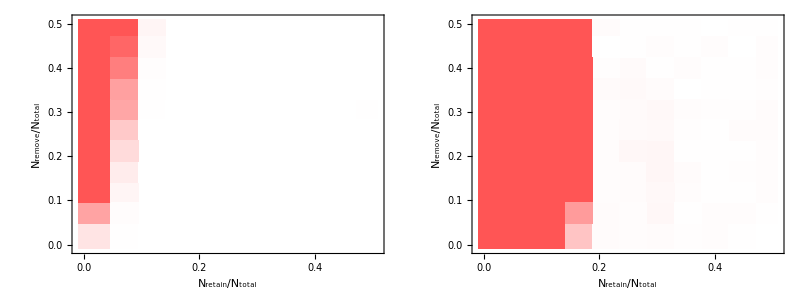

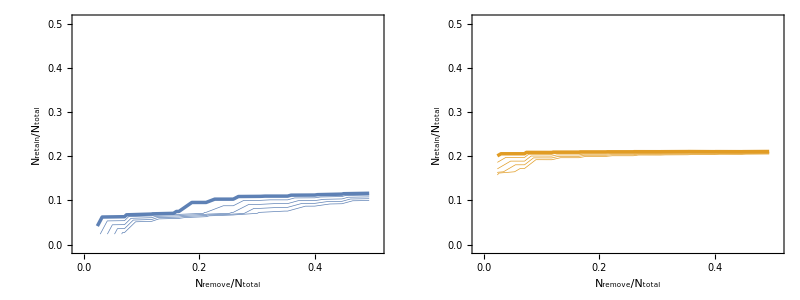

data/reaction3.dat

data/reaction4.dat

```mathematica
test1={#[[1]],#[[2]],Count[#[[3]],u_/;u>Log[2.0]/Log[10]]/Length[#[[3]]]}&/@DeleteCases[Flatten[Table[{keep/nreactions,remove/nreactions,Abs[Log[Cases[rlst1,u_/;First[u]==678&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]/Log[10]]},{keep,40, 840, 80},{remove,40, 840, 80}],1],u_/;Last[u]=={}];
test2={#[[1]],#[[2]],Count[#[[3]],u_/;u>Log[2.0]/Log[10]]/Length[#[[3]]]}&/@DeleteCases[Flatten[Table[{keep/nreactions,remove/nreactions,Abs[Log[Cases[rlst1,u_/;First[u]==683&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]/Log[10]]},{keep,40, 840, 80},{remove,40, 840, 80}],1],u_/;Last[u]=={}];
Grid[{{ListDensityPlot[test1,InterpolationOrder->0,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunction->(Blend[{White,Lighter[Red]},#/(0.2)]&),ColorFunctionScaling->False,FrameLabel->{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]]},LabelStyle->Directive[16,Black],FrameStyle->Black,ImageSize->250,ImagePadding->{{55,5},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}}],ListDensityPlot[test2,InterpolationOrder->0,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunction->(Blend[{White,Lighter[Red]},#/(0.2)]&),ColorFunctionScaling->False,FrameLabel->{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]]},LabelStyle->Directive[16,Black],FrameStyle->Black,ImageSize->250,ImagePadding->{{55,5},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}}]}}]
Grid[{{ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test1,InterpolationOrder->1,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,5},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.02,0.1,0.02}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]],ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test2,InterpolationOrder->1,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,5},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.02,0.1,0.02}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]]}}]
Export["data/reaction3.dat", test1]
Export["data/reaction4.dat",test2]
```

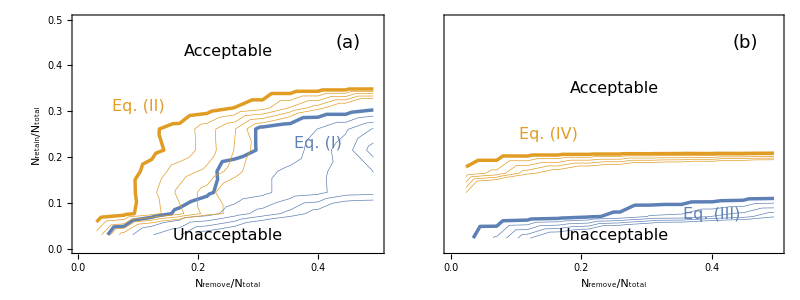

```mathematica
test1=ToExpression[Import["data/reaction1.dat"]];
test2=ToExpression[Import["data/reaction2.dat"]];
test3=ToExpression[Import["data/reaction3.dat"]];
test4=ToExpression[Import["data/reaction4.dat"]];
p1=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test1,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],"Combustion"}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{55,10},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]];
p2=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test2,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,10},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]];
p3=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test3,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{None,None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],"Pyrolysis"}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{10,55},{55,55}},FrameTicks->{{Table[{i,""},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]];
p4=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test4,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{None,None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{10,55},{55,5}},FrameTicks->{{Table[{i,""},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]];
p=Grid[{{Show[p1,p2,Epilog->{Inset[Style["Acceptable",16],{0.25,0.43}],Inset[Style["Unacceptable",16],{0.25,0.03}],Inset[Style["Eq. (I)",Directive[16,ColorData[97,"ColorList"][[1]]]],{0.4,0.23},Background->White],Inset[Style["Eq. (II)", Directive[16,ColorData[97,"ColorList"][[2]]]],{0.1,0.31},Background->White],Inset[Style["(a)",18],{0.45,0.45}]},PlotRange->{{0,0.5},{0,0.5}}],Show[p3,p4,Epilog->{Inset[Style["Acceptable",16],{0.25,0.35}],Inset[Style["Unacceptable",16],{0.25,0.03}],Inset[Style["Eq. (III)",Directive[16,ColorData[97,"ColorList"][[1]]],Background->White],{0.4,0.075}],Inset[Style["Eq. (IV)",Directive[16,ColorData[97,"ColorList"][[2]]],Background->White],{0.15,0.25}],Inset[Style["(b)",18],{0.45,0.45}]},PlotRange->{{0,0.5},{0,0.5}}]}}]
```